### Start choosing the example:

```mathematica
t=2;
beta=0;
A=0.2;
g[x]
```

Log[x]

```mathematica
Data=DataG[t]
```

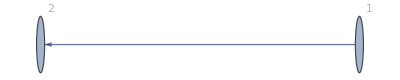
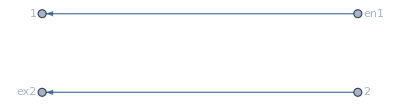
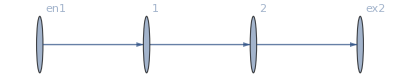
<|Vertices List→{1,2},Adjacency Matrix→{{0,1},{0,0}},Entrance Vertices and Currents→{{1,80}},Exit Vertices and Terminal Costs→{{2,0}},Switching Costs→{},VL→{1,2},AM→{{0,1},{0,0}},EVC→{{1,80}},EVTC→{{2,0}},SC→{},BG→-Graphics-,EntranceVertices→{1},InwardVertices→<|1→en1|>,ExitVertices→{2},OutwardVertices→<|2→ex2|>,InEdges→{en1->1},OutEdges→{2->ex2},AuxiliaryGraph→-Graphics-,FG→-Graphics-,EL→{1->2,2->ex2,en1->1},BEL→{1->2},FVL→{1,2,en1,ex2},jargs→{{1,1->2},{2,1->2},{2,2->ex2},{ex2,2->ex2},{en1,en1->1},{1,en1->1}},uargs→{{1,1->2},{2,1->2},{2,2->ex2},{ex2,2->ex2},{en1,en1->1},{1,en1->1}},AllTransitions→{},EntryArgs→{{1,en1->1}},EntryDataAssociation→<|{1,en1->1}→80|>,ExitCosts→<|ex2→0|>,js→{j1,j2,j3,j4,j5,j6},jvars→<|{1,1->2}→j1,{2,1->2}→j2,{2,2->ex2}→j3,{ex2,2->ex2}→j4,{en1,en1->1}→j5,{1,en1->1}→j6|>,us→{u1,u2,u3,u4,u5,u6},uvars→<|{1,1->2}→u1,{2,1->2}→u2,{2,2->ex2}→u3,{ex2,2->ex2}→u4,{en1,en1->1}→u5,{1,en1->1}→u6|>,jts→{},jtvars→<||>,SignedCurrents→<|1->2→-j1+j2|>,SwitchingCosts→<||>,EqPosJs→j1≥0&&j2≥0&&j3≥0&&j4≥0&&j5≥0&&j6≥0,EqPosJts→True,EqCurrentCompCon→(j1==0||j2==0)&&(j3==0||j4==0)&&(j5==0||j6==0),EqTransitionCompCon→True,NoDeadEnds→{{1,1->2},{2,1->2}},EqBalanceSplittingCurrents→j1==0&&j2==0,BalanceSplittingCurrents→{j1,j2},NoDeadStarts→{{2,1->2},{1,1->2}},RuleBalanceGatheringCurrents→{j2→0,j1→0},BalanceGatheringCurrents→{-j2,-j1},EqBalanceGatheringCurrents→j2==0&&j1==0,EqEntryIn→{j6==80},RuleEntryOut→{j5→0},RuleExitCurrentsIn→{j3→0},RuleExitValues→{u4→0},EqValueAuxiliaryEdges→u5==u6&&u3==u4,OutRules→{{2,2->ex2,1->2}→∞,{2,2->ex2,2->ex2}→∞,{2,2->ex2,en1->1}→∞},InRules→{{1,1->2,en1->1}→∞,{1,en1->1,en1->1}→∞},EqSwitchingByVertex→{{},{}},EqCompCon→True,Nlhs→{-j1+j2-u1+u2}|>

The matrices B and K are: 
{(80
0
0),(0 | 0 | 1
1 | -1 | 0
-1 | 1 | 0)}
The order of the variables is 
{j1,j2,j6}

{SparseArray[…],SparseArray[…],{j1,j2,j6}}

EqBalanceSplittingCurrents: j1==0&&j2==0

EqCurrentCompCon: (j1==0||j2==0)&&(j3==0||j4==0)&&(j5==0||j6==0)

True<|j6→80,j5→0,j3→0,j2→0,j1→0|>

EqTransitionCompCon: True

True<|j6→80,j5→0,j3→0,j2→0,j1→0|>

EqPosJs: j1≥0&&j2≥0&&j3≥0&&j4≥0&&j5≥0&&j6≥0

j4≥0<|j6→80,j5→0,j3→0,j2→0,j1→0|>

EqPosJts: True

True<|j6→80,j5→0,j3→0,j2→0,j1→0|>

EqValueAuxiliaryEdges: u5==u6&&u3==u4

True<|j6→80,j5→0,j3→0,j2→0,j1→0,u4→0,u3→0,u6→u5|>

EqSwitchingByVertex: {{},{}}

True{}

EqCompCon: True

True<||>

{j4≥0,<|u4→u3,u6→u5|>}

Preprocessing done!

1: TrueTrue

2: TrueTrue

3: j4≥0j4≥0

4: TrueTrue

5: TrueTrue

6: TrueTrue

<|u2→j1-j2+u1|>

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/D2E2.m"]
Data=<|"Vertices List"->{1,2},"Adjacency Matrix"->{{0,1},{0,0}},"Entrance Vertices and Currents"->{{1,I1}},"Exit Vertices and Terminal Costs"->{{2,U1}},"Switching Costs"->{}|>;
d2e=Data2Equations[Data/.{I1-> 80, U1-> 0}]
GetKirchhoffMatrix[d2e]
CriticalCongestionSolver[d2e]
```

```mathematica
SparseArray[…].DiagonalMatrix[j].Transpose@SparseArray[…]//MatrixForm
```

(j6 | 0 | j6 | 0 | 0
0 | j1+j2+jt1+jt2 | -jt1-jt2 | -j1-j2 | 0
j6 | -jt1-jt2 | j6+jt1+jt2 | 0 | 0
0 | -j1-j2 | 0 | j1+j2+jt3+jt4 | -jt3-jt4
0 | 0 | 0 | -jt3-jt4 | j4+jt3+jt4)

```mathematica
Reduce
```

```mathematica
CriticalCongestionSolver[d2e]
```

EqBalanceSplittingCurrents: j1==jt1&&j6==jt2&&j2==jt3&&j3==jt4

EqCurrentCompCon: (j1==0||j2==0)&&(j3==0||j4==0)&&(j5==0||j6==0)

True<|j6→80,j5→0,j3→0,j2→80,j1→0,j4→80,jt1→0,jt2→80,jt3→80,jt4→0|>

EqTransitionCompCon: (jt1==0||jt2==0)&&(jt3==0||jt4==0)

True<|j6→80,j5→0,j3→0,j2→80,j1→0,j4→80,jt1→0,jt2→80,jt3→80,jt4→0|>

EqPosJs: j1≥0&&j2≥0&&j3≥0&&j4≥0&&j5≥0&&j6≥0

True<|j6→80,j5→0,j3→0,j2→80,j1→0,j4→80,jt1→0,jt2→80,jt3→80,jt4→0|>

EqPosJts: jt1≥0&&jt2≥0&&jt3≥0&&jt4≥0

True<|j6→80,j5→0,j3→0,j2→80,j1→0,j4→80,jt1→0,jt2→80,jt3→80,jt4→0|>

EqValueAuxiliaryEdges: u5==u6&&u3==u4

True<|j6→80,j5→0,j3→0,j2→80,j1→0,j4→80,jt1→0,jt2→80,jt3→80,jt4→0,u4→0,u3→0,u6→u5|>

EqSwitchingByVertex: {{u1≤u6,u6≤u1},{u2≤u3,u3≤u2}}

u1≤u1&&u1≤u1<|j6→80,j5→0,j3→0,j2→80,j1→0,j4→80,jt1→0,jt2→80,jt3→80,jt4→0,u4→0,u3→0,u6→u1,u5→u1,u2→0|>

EqCompCon: (jt1==0||-u1+u6==0)&&(jt2==0||u1-u6==0)&&(jt3==0||-u2+u3==0)&&(jt4==0||u2-u3==0)

True<|j6→80,j5→0,j3→0,j2→80,j1→0,j4→80,jt1→0,jt2→80,jt3→80,jt4→0,u4→0,u3→0,u6→u1,u5→u1,u2→0|>

Preprocessing done!

1: TrueTrue

2: TrueTrue

3: TrueTrue

4: TrueTrue

5: TrueTrue

6: TrueTrue

<|j6→80,j5→0,j3→0,j2→80,j1→0,j4→80,jt1→0,jt2→80,jt3→80,jt4→0,u4→0,u3→0,u6→80,u5→80,u2→0,u1→80|>

```mathematica
MFGPreprocessing[d2e]
```

EqBalanceSplittingCurrents: j1==jt1&&j6==jt2&&j2==jt3&&j3==jt4

EqCurrentCompCon: (j1==0||j2==0)&&(j3==0||j4==0)&&(j5==0||j6==0)

True<|j6→80,j5→0,j3→0,j2→80,j1→0,j4→80,jt1→0,jt2→80,jt3→80,jt4→0|>

EqTransitionCompCon: (jt1==0||jt2==0)&&(jt3==0||jt4==0)

True<|j6→80,j5→0,j3→0,j2→80,j1→0,j4→80,jt1→0,jt2→80,jt3→80,jt4→0|>

EqPosJs: j1≥0&&j2≥0&&j3≥0&&j4≥0&&j5≥0&&j6≥0

True<|j6→80,j5→0,j3→0,j2→80,j1→0,j4→80,jt1→0,jt2→80,jt3→80,jt4→0|>

EqPosJts: jt1≥0&&jt2≥0&&jt3≥0&&jt4≥0

True<|j6→80,j5→0,j3→0,j2→80,j1→0,j4→80,jt1→0,jt2→80,jt3→80,jt4→0|>

EqValueAuxiliaryEdges: u5==u6&&u3==u4

True<|j6→80,j5→0,j3→0,j2→80,j1→0,j4→80,jt1→0,jt2→80,jt3→80,jt4→0,u4→0,u3→0,u6→u5|>

EqSwitchingByVertex: {{u1≤u6,u6≤u1},{u2≤u3,u3≤u2}}

u1≤u1&&u1≤u1<|j6→80,j5→0,j3→0,j2→80,j1→0,j4→80,jt1→0,jt2→80,jt3→80,jt4→0,u4→0,u3→0,u6→u1,u5→u1,u2→0|>

EqCompCon: (jt1==0||-u1+u6==0)&&(jt2==0||u1-u6==0)&&(jt3==0||-u2+u3==0)&&(jt4==0||u2-u3==0)

True<|j6→80,j5→0,j3→0,j2→80,j1→0,j4→80,jt1→0,jt2→80,jt3→80,jt4→0,u4→0,u3→0,u6→u1,u5→u1,u2→0|>

<|Vertices List→{1,2},Adjacency Matrix→{{0,1},{0,0}},Entrance Vertices and Currents→{{1,80}},Exit Vertices and Terminal Costs→{{2,0}},Switching Costs→{},VL→{1,2},AM→{{0,1},{0,0}},EVC→{{1,80}},EVTC→{{2,0}},SC→{},BG→-Graphics-,EntranceVertices→{1},InwardVertices→<|1→en1|>,ExitVertices→{2},OutwardVertices→<|2→ex2|>,InEdges→{en1->1},OutEdges→{2->ex2},AuxiliaryGraph→-Graphics-,FG→-Graphics-,EL→{1->2,2->ex2,en1->1},BEL→{1->2},FVL→{1,2,en1,ex2},jargs→{{1,1->2},{2,1->2},{2,2->ex2},{ex2,2->ex2},{en1,en1->1},{1,en1->1}},uargs→{{1,1->2},{2,1->2},{2,2->ex2},{ex2,2->ex2},{en1,en1->1},{1,en1->1}},AllTransitions→{{1,1->2,en1->1},{1,en1->1,1->2},{2,1->2,2->ex2},{2,2->ex2,1->2}},EntryArgs→{{1,en1->1}},EntryDataAssociation→<|{1,en1->1}→80|>,ExitCosts→<|ex2→0|>,js→{j1,j2,j3,j4,j5,j6},jvars→<|{1,1->2}→j1,{2,1->2}→j2,{2,2->ex2}→j3,{ex2,2->ex2}→j4,{en1,en1->1}→j5,{1,en1->1}→j6|>,us→{u1,u2,u3,u4,u5,u6},uvars→<|{1,1->2}→u1,{2,1->2}→u2,{2,2->ex2}→u3,{ex2,2->ex2}→u4,{en1,en1->1}→u5,{1,en1->1}→u6|>,jts→{jt1,jt2,jt3,jt4},jtvars→<|{1,1->2,en1->1}→jt1,{1,en1->1,1->2}→jt2,{2,1->2,2->ex2}→jt3,{2,2->ex2,1->2}→jt4|>,SignedCurrents→<|1->2→-j1+j2|>,SwitchingCosts→<|{1,1->2,en1->1}→0,{1,en1->1,1->2}→0,{2,1->2,2->ex2}→0,{2,2->ex2,1->2}→0|>,EqPosJs→True,EqPosJts→True,EqCurrentCompCon→True,EqTransitionCompCon→True,NoDeadEnds→{{1,1->2},{1,en1->1},{2,1->2},{2,2->ex2}},EqBalanceSplittingCurrents→j1==jt1&&j6==jt2&&j2==jt3&&j3==jt4,BalanceSplittingCurrents→{j1-jt1,j6-jt2,j2-jt3,j3-jt4},NoDeadStarts→{{2,1->2},{en1,en1->1},{1,1->2},{ex2,2->ex2}},RuleBalanceGatheringCurrents→{j2→jt2,j5→jt1,j1→jt4,j4→jt3},BalanceGatheringCurrents→{-j2+jt2,-j5+jt1,-j1+jt4,-j4+jt3},EqBalanceGatheringCurrents→j2==jt2&&j5==jt1&&j1==jt4&&j4==jt3,EqEntryIn→{j6==80},RuleEntryOut→{j5→0},RuleExitCurrentsIn→{j3→0},RuleExitValues→{u4→0},EqValueAuxiliaryEdges→u5==u6&&u3==u4,OutRules→{{2,2->ex2,1->2}→∞,{2,2->ex2,2->ex2}→∞,{2,2->ex2,en1->1}→∞},InRules→{{1,1->2,en1->1}→∞,{1,en1->1,en1->1}→∞},EqSwitchingByVertex→u1≤u1&&u1≤u1,EqCompCon→True,Nlhs→{-j1+j2-u1+u2},InitRules→<|j6→80,j5→0,j3→0,j2→80,j1→0,j4→80,jt1→0,jt2→80,jt3→80,jt4→0,u4→0,u3→0,u6→u1,u5→u1,u2→0|>,TrueEq→True,RuleSwitchingByVertex→{u5→u1,u2→0}|>

```mathematica
<|"Vertices List"->{1,2},"Adjacency Matrix"->{{0,1},{0,0}},"Entrance Vertices and Currents"->{{1,80}},"Exit Vertices and Terminal Costs"->{{2,0}},"Switching Costs"->{},"VL"->{1,2},"AM"->{{0,1},{0,0}},"EVC"->{{1,80}},"EVTC"->{{2,0}},"SC"->{},"BG"->-Graphics-,"EntranceVertices"->{1},"InwardVertices"-><|1->en1|>,"ExitVertices"->{2},"OutwardVertices"-><|2->ex2|>,"InEdges"->{en1->1},"OutEdges"->{2->ex2},"AuxiliaryGraph"->-Graphics-,"FG"->-Graphics-,"EL"->{1->2,2->ex2,en1->1},"BEL"->{1->2},"FVL"->{1,2,en1,ex2},"jargs"->{{1,1->2},{2,1->2},{2,2->ex2},{ex2,2->ex2},{en1,en1->1},{1,en1->1}},"uargs"->{{1,1->2},{2,1->2},{2,2->ex2},{ex2,2->ex2},{en1,en1->1},{1,en1->1}},"AllTransitions"->{{1,1->2,en1->1},{1,en1->1,1->2},{2,1->2,2->ex2},{2,2->ex2,1->2}},"EntryArgs"->{{1,en1->1}},"EntryDataAssociation"-><|{1,en1->1}->80|>,"ExitCosts"-><|ex2->0|>,"js"->{j1,j2,j3,j4,j5,j6},"jvars"-><|{1,1->2}->j1,{2,1->2}->j2,{2,2->ex2}->j3,{ex2,2->ex2}->j4,{en1,en1->1}->j5,{1,en1->1}->j6|>,"us"->{u1,u2,u3,u4,u5,u6},"uvars"-><|{1,1->2}->u1,{2,1->2}->u2,{2,2->ex2}->u3,{ex2,2->ex2}->u4,{en1,en1->1}->u5,{1,en1->1}->u6|>,"jts"->{jt1,jt2,jt3,jt4},"jtvars"-><|{1,1->2,en1->1}->jt1,{1,en1->1,1->2}->jt2,{2,1->2,2->ex2}->jt3,{2,2->ex2,1->2}->jt4|>,"SignedCurrents"-><|1->2->-j1+j2|>,"SwitchingCosts"-><|{1,1->2,en1->1}->0,{1,en1->1,1->2}->0,{2,1->2,2->ex2}->0,{2,2->ex2,1->2}->0|>,"EqPosJs"->True,"EqPosJts"->True,"EqCurrentCompCon"->True,"EqTransitionCompCon"->True,"NoDeadEnds"->{{1,1->2},{1,en1->1},{2,1->2},{2,2->ex2}},"EqBalanceSplittingCurrents"->j1==jt1&&j6==jt2&&j2==jt3&&j3==jt4,"BalanceSplittingCurrents"->{j1-jt1,j6-jt2,j2-jt3,j3-jt4},"NoDeadStarts"->{{2,1->2},{en1,en1->1},{1,1->2},{ex2,2->ex2}},"RuleBalanceGatheringCurrents"->{j2->jt2,j5->jt1,j1->jt4,j4->jt3},"BalanceGatheringCurrents"->{-j2+jt2,-j5+jt1,-j1+jt4,-j4+jt3},"EqBalanceGatheringCurrents"->j2==jt2&&j5==jt1&&j1==jt4&&j4==jt3,"EqEntryIn"->{j6==80},"RuleEntryOut"->{j5->0},"RuleExitCurrentsIn"->{j3->0},"RuleExitValues"->{u4->0},"EqValueAuxiliaryEdges"->u5==u6&&u3==u4,"OutRules"->{{2,2->ex2,1->2}->∞,{2,2->ex2,2->ex2}->∞,{2,2->ex2,en1->1}->∞},"InRules"->{{1,1->2,en1->1}->∞,{1,en1->1,en1->1}->∞},"EqSwitchingByVertex"->u1≤u5&&u5≤u1&&u2≤0&&0≤u2,"EqCompCon"->True,"Nlhs"->{-j1+j2-u1+u2},"InitRules"-><|j6->80,j5->0,j3->0,j2->80,j1->0,j4->80,jt1->0,jt2->80,jt3->80,jt4->0,u4->0,u3->0,u6->u1,u2->0,u5->u1|>,"TrueEq"->True|>/.<|j6->80,j5->0,j3->0,j2->80,j1->0,j4->80,jt1->0,jt2->80,jt3->80,jt4->0,u4->0,u3->0,u6->u1,u2->0,u5->u1|>
```

<|Vertices List→{1,2},Adjacency Matrix→{{0,1},{0,0}},Entrance Vertices and Currents→{{1,80}},Exit Vertices and Terminal Costs→{{2,0}},Switching Costs→{},VL→{1,2},AM→{{0,1},{0,0}},EVC→{{1,80}},EVTC→{{2,0}},SC→{},BG→-Graphics-,EntranceVertices→{1},InwardVertices→<|1→en1|>,ExitVertices→{2},OutwardVertices→<|2→ex2|>,InEdges→{en1->1},OutEdges→{2->ex2},AuxiliaryGraph→-Graphics-,FG→-Graphics-,EL→{1->2,2->ex2,en1->1},BEL→{1->2},FVL→{1,2,en1,ex2},jargs→{{1,1->2},{2,1->2},{2,2->ex2},{ex2,2->ex2},{en1,en1->1},{1,en1->1}},uargs→{{1,1->2},{2,1->2},{2,2->ex2},{ex2,2->ex2},{en1,en1->1},{1,en1->1}},AllTransitions→{{1,1->2,en1->1},{1,en1->1,1->2},{2,1->2,2->ex2},{2,2->ex2,1->2}},EntryArgs→{{1,en1->1}},EntryDataAssociation→<|{1,en1->1}→80|>,ExitCosts→<|ex2→0|>,js→{0,80,0,80,0,80},jvars→<|{1,1->2}→0,{2,1->2}→80,{2,2->ex2}→0,{ex2,2->ex2}→80,{en1,en1->1}→0,{1,en1->1}→80|>,us→{u1,0,0,0,u1,u1},uvars→<|{1,1->2}→u1,{2,1->2}→0,{2,2->ex2}→0,{ex2,2->ex2}→0,{en1,en1->1}→u1,{1,en1->1}→u1|>,jts→{0,80,80,0},jtvars→<|{1,1->2,en1->1}→0,{1,en1->1,1->2}→80,{2,1->2,2->ex2}→80,{2,2->ex2,1->2}→0|>,SignedCurrents→<|1->2→-0+80|>,SwitchingCosts→<|{1,1->2,en1->1}→0,{1,en1->1,1->2}→0,{2,1->2,2->ex2}→0,{2,2->ex2,1->2}→0|>,EqPosJs→True,EqPosJts→True,EqCurrentCompCon→True,EqTransitionCompCon→True,NoDeadEnds→{{1,1->2},{1,en1->1},{2,1->2},{2,2->ex2}},EqBalanceSplittingCurrents→0==0&&80==80&&80==80&&0==0,BalanceSplittingCurrents→{0-0,80-80,80-80,0-0},NoDeadStarts→{{2,1->2},{en1,en1->1},{1,1->2},{ex2,2->ex2}},RuleBalanceGatheringCurrents→{80→80,0→0,0→0,80→80},BalanceGatheringCurrents→{-80+80,-0+0,-0+0,-80+80},EqBalanceGatheringCurrents→80==80&&0==0&&0==0&&80==80,EqEntryIn→{80==80},RuleEntryOut→{0→0},RuleExitCurrentsIn→{0→0},RuleExitValues→{0→0},EqValueAuxiliaryEdges→u1==u1&&0==0,OutRules→{{2,2->ex2,1->2}→∞,{2,2->ex2,2->ex2}→∞,{2,2->ex2,en1->1}→∞},InRules→{{1,1->2,en1->1}→∞,{1,en1->1,en1->1}→∞},EqSwitchingByVertex→u1≤u1&&u1≤u1&&0≤0&&0≤0,EqCompCon→True,Nlhs→{-0+80-u1+0},InitRules→<|j6→80,j5→0,j3→0,j2→80,j1→0,j4→80,jt1→0,jt2→80,jt3→80,jt4→0,u4→0,u3→0,u6→u1,u2→0,u5→u1|>,TrueEq→True|>

```mathematica
(rule=CriticalCongestionSolver2[d2e=D2E[Data/.{I1-> 80, U1-> 15}]])//AbsoluteTiming
```

Variables are all set

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the critical case equations

Expanding critical rules...

EliminateVarsSimplify for the us

Finished with the us!

Done!

{0.051257,<|u1→95,u2→15,u3→15,u4→15,u5→95,u6→95,j1→0,j2→80,j3→0,j4→80,j5→0,j6→80|>}

```mathematica
(rule=CriticalCongestionSolver2[d2e])//AbsoluteTiming
```

EliminateVarsSimplify for the us

Finished with the us!

Done!

{0.003981,<|u1→95,u2→15,u3→15,u4→15,u5→95,u6→95,j1→0,j2→80,j3→0,j4→80,j5→0,j6→80|>}

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2},Adjacency Matrix→{{0,1},{0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{2,U1}},Switching Costs→{}|>

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: {NonNegative[j5707]&&NonNegative[j5708]&&NonNegative[j5709]&&NonNegative[j5710]&&NonNegative[j5711]&&NonNegative[j5712]&&NonNegative[jt5713]&&NonNegative[jt5714]&&NonNegative[jt5715]&&NonNegative[jt5716]&&j5710==jt5713&&j5709==jt5714&&j5707==jt5715&&j5711==jt5716&&j5707==jt5714&&j5712==jt5713&&j5710==jt5716&&j5708==jt5715&&j5709==80&&u5721==15&&NonNegative[u5717-u5722]&&NonNegative[u5718-u5720]&&-u5719+u5722==0&&-u5718+u5721==0&&(j5710==0||j5707==0)&&(j5711==0||j5708==0)&&(j5712==0||j5709==0)&&(jt5713==0||jt5714==0)&&(jt5715==0||jt5716==0)&&jt5713==0&&(jt5714==0||-u5717+u5722==0)&&(jt5715==0||-u5718+u5720==0)&&jt5716==0&&j5707-j5710-u5717+u5720==0,{j5709→80,u5721→15}}

DataToEquations: It took 1.×10^-6 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.009127,Null}

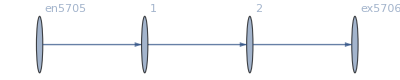

<|j5707→80,j5708→80,j5709→80,j5710→0,j5711→0,j5712→0,jt5713→0,jt5714→80,jt5715→80,jt5716→0,u5717→95,u5718→15,u5719→95,u5720→15,u5721→15,u5722→95|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->80,U1->15}];//Timing
MFGEquations["FG"]
MFGEquations["criticalreduced1"][[2]]//KeySort
```

#### Non-linear case

```mathematica
alpha=0;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

EEX: newrules when Head is Equal: {{u51→17.582}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.14725×10^-17

EEX: newrules when Head is Equal: {{u51→17.582}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.14725×10^-17

<|j41→80,j42→80,j43→80,j44→0.,j45→0.,j46→0.,jt47→0.,jt48→80,jt49→80,jt50→0.,u51→17.582,u52→15.,u53→17.582,u54→15.,u55→15.,u56→17.582|>

```mathematica
alpha=0.1;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

EEX: newrules when Head is Equal: {{u51→18.1613}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.6236×10^-17

EEX: newrules when Head is Equal: {{u51→18.1613}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.6236×10^-17

<|j41→80,j42→80,j43→80,j44→0.,j45→0.,j46→0.,jt47→0.,jt48→80,jt49→80,jt50→0.,u51→18.1613,u52→15.,u53→18.1613,u54→15.,u55→15.,u56→18.1613|>

```mathematica
alpha=0.3;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

EEX: newrules when Head is Equal: {{u51→20.0239}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.10769×10^-17

EEX: newrules when Head is Equal: {{u51→20.0239}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.10769×10^-17

<|j41→80,j42→80,j43→80,j44→0.,j45→0.,j46→0.,jt47→0.,jt48→80,jt49→80,jt50→0.,u51→20.0239,u52→15.,u53→20.0239,u54→15.,u55→15.,u56→20.0239|>

```mathematica
alpha=1;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,
SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: newrules when Head is Equal: {{u51→95.}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[8.52651×10^-14,ComplexInfinity]

<|j41→80,j42→80,j43→80,j44→0.,j45→0.,j46→0.,jt47→0.,jt48→80,jt49→80,jt50→0.,u51→95.,u52→15.,u53→95.,u54→15.,u55→15.,u56→95.|>

```mathematica
alpha=1.2;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

EEX: newrules when Head is Equal: {{u51→378.906}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

EEX: newrules when Head is Equal: {{u51→378.906}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j41→80,j42→80,j43→80,j44→0.,j45→0.,j46→0.,jt47→0.,jt48→80,jt49→80,jt50→0.,u51→378.906,u52→15.,u53→378.906,u54→15.,u55→15.,u56→378.906|>

```mathematica
alpha=1.6;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

EEX: newrules when Head is Equal: {{u51→290058.}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

EEX: newrules when Head is Equal: {{u51→290058.}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j41→80,j42→80,j43→80,j44→0.,j45→0.,j46→0.,jt47→0.,jt48→80,jt49→80,jt50→0.,u51→290058.,u52→15.,u53→290058.,u54→15.,u55→15.,u56→290058.|>

```mathematica
alpha=1.7;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

EEX: newrules when Head is Equal: {{u51→1.5595×10^7}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

EEX: newrules when Head is Equal: {{u51→1.5595×10^7}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j41→80,j42→80,j43→80,j44→0.,j45→0.,j46→0.,jt47→0.,jt48→80,jt49→80,jt50→0.,u51→1.5595×10^7,u52→15.,u53→1.5595×10^7,u54→15.,u55→15.,u56→1.5595×10^7|>

```mathematica
alpha=1.8;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

EEX: newrules when Head is Equal: {{u51→2.40526×10^10}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

EEX: newrules when Head is Equal: {{u51→2.40526×10^10}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j41→80,j42→80,j43→80,j44→0.,j45→0.,j46→0.,jt47→0.,jt48→80,jt49→80,jt50→0.,u51→2.40526×10^10,u52→15.,u53→2.40526×10^10,u54→15.,u55→15.,u56→2.40526×10^10|>

```mathematica
alpha=1.9;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

EEX: newrules when Head is Equal: {{u51→5.6037×10^18}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

EEX: newrules when Head is Equal: {{u51→5.6037×10^18}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j41→80,j42→80,j43→80,j44→0.,j45→0.,j46→0.,jt47→0.,jt48→80,jt49→80,jt50→0.,u51→5.6037×10^18,u52→15.,u53→5.6037×10^18,u54→15.,u55→15.,u56→5.6037×10^18|>

```mathematica
alpha=2;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

EEX: newrules when Head is Equal: {{u51→2.2049×10^106}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

EEX: newrules when Head is Equal: {{u51→2.2049×10^106}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j41→80,j42→80,j43→80,j44→0.,j45→0.,j46→0.,jt47→0.,jt48→80,jt49→80,jt50→0.,u51→2.2049×10^106,u52→15.,u53→2.2049×10^106,u54→15.,u55→15.,u56→2.2049×10^106|>

```mathematica
RowReduce@({{0, 0, 0, 1, 0, 0, 0, 0}, {1, -1, 0, 0, -1, 1, 0, 0}, {0, 0, 0, 1, 1, -1, 0, 0}, {-1, 1, 0, 0, 0, 0, -1, 1}, {0, 0, -1, 0, 0, 0, 1, -1}})
```

{{1,-1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,-1,0,0},{0,0,0,0,0,0,1,-1}}

```mathematica
$Context
```

Global`

```mathematica
NDSolve
```

```mathematica
ToString/@{InitRules,RuleBalanceGatheringCurrents,EqEntryIn,RuleEntryOut,TrueEq,RuleExitCurrentsIn,RuleExitValues,EqValueAuxiliaryEdges,EqSwitchingByVertex,EqCompCon,EqBalanceSplittingCurrents,EqCurrentCompCon,EqTransitionCompCon,EqPosJs,EqPosJts,ModuleVarsNames}
```

{InitRules,RuleBalanceGatheringCurrents,EqEntryIn,RuleEntryOut,TrueEq,RuleExitCurrentsIn,RuleExitValues,EqValueAuxiliaryEdges,EqSwitchingByVertex,EqCompCon,EqBalanceSplittingCurrents,EqCurrentCompCon,EqTransitionCompCon,EqPosJs,EqPosJts,ModuleVarsNames}